```mathematica
ClearAll["Global`*"]
```

```mathematica
pde=D[T[x,t],t]==f ∂_x [D[T[x,t], x]]
soln=DSolve[pde,T[x,t],{x,t}]
```

Syntax::sntxf: "D[" cannot be followed by "[∂_x T[x, t]], x]".

Syntax::tsntxi: "[∂_x T[x, t]]" is incomplete; more input is needed.

Syntax::sntxi: Incomplete expression; more input is needed.

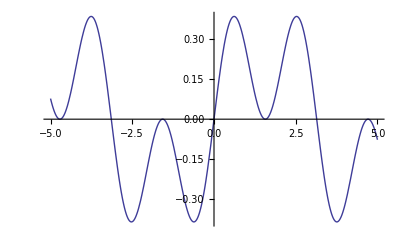

```mathematica
Plot[Sin[x]Cos[x]^2,{x,-5,5}]
```

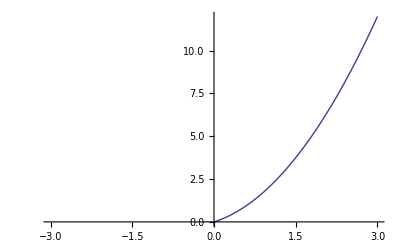

```mathematica
Plot[x(1+Abs[x]),{x,-3,3},PlotRange->{0,12}]
```